# Neural Logic Networks

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
Manipulate[RealToOneHot[x, {-10,20},16],{x,-10,20}]
```

```mathematica
fl=FunctionLayer[BinaryToReal[8,{-10,20}]]
```

FunctionLayer[<>]

```mathematica
brl=BinaryToRealLayer[8,{-10,20}]
```

NetGraph[<>]

```mathematica
a={fl[{1,1,1,0,1,1,1,0}],brl[{0.6,1,0.9,0.3,1,1,1,0}]}
```

{{17.8906},{17.8906}}

```mathematica
b={fl[{0,0,0,1,0,0,0,0}],brl[{0,0,0.01,0.99,0,0,0,0}]}
```

{{-8.125},{-8.125}}

```mathematica
aa=RealToBinary[a[[1]],{-10,20},8]
```

{{1,1,1,0,1,1,1,0}}

```mathematica
bb=RealToBinary[b[[1]],{-10,20},8]
```

{{0,0,0,1,0,0,0,0}}

## A regression problem

```mathematica
data=ResourceData["7307b047-05ec-4d46-b3c9-9995faf75130"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

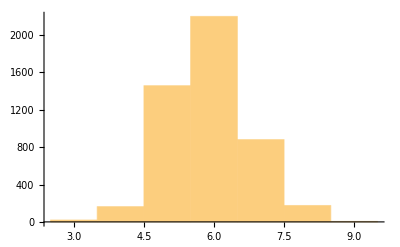

```mathematica
Histogram[#["WineQuality"]&/@data]
```

## Utilities

### Feature encoders

```mathematica
standardizer=FeatureExtraction[KeyDrop["WineQuality"]@trainData,"StandardizedVector"]
```

FeatureExtractorFunction[…]

```mathematica
StandardizeData[data_,targetName_,standardizer_]:=Block[
{
featureData=KeyDrop[targetName]@data,
targetData=KeyTake[targetName]@data,
standardizedFeatureData,
featureNames
},
standardizedFeatureData=standardizer[featureData];
featureNames=Flatten[Normal[DeleteDuplicates[Keys[featureData]]]];standardizedFeatureData=Map[<|Map[First[#]->Last[#]&,Partition[Riffle[featureNames,#],2]]|>&,standardizedFeatureData];
Dataset[Merge[#,First]&/@Partition[Riffle[standardizedFeatureData,Normal[targetData]],2]]
]
```

```mathematica
standardizedTrainData=StandardizeData[trainData,"WineQuality",standardizer];
```

```mathematica
standardizedTestData=StandardizeData[testData,"WineQuality",standardizer];
```

```mathematica
FeatureValues[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->Last[#]&/@featureValues]
]
featureValues=FeatureValues[standardizedTrainData];
```

```mathematica
encoders=Map[RealEncoderDecoder[#]&,featureValues];
```

```mathematica
standardNetInputSize=Length[encoders]-1
```

11

```mathematica
standardFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],-1]},NetGraph[
<|
Splice[Map[#->ReshapeLayer[{1},"Input"->{}]&,Keys[inputEncoders]]],
"Catenate"->CatenateLayer["Output"->standardNetInputSize]
|>,
Join[
Map[#->"Catenate"&,Keys[inputEncoders]],
Map[NetPort[#]->#&,Keys[inputEncoders]]
]
]]
```

NetGraph[<>]

```mathematica
neuralLogicFeatureLayer=Block[{inputEncoders=Drop[Normal[encoders],-1]},NetGraph[
<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[#]->"Catenate"&,Keys[inputEncoders]],
Sequence@@Normal[Drop[Normal[#["NetEncoder"]&/@encoders],-1]]
]]
```

NetGraph[<>]

```mathematica
exampleInputFeature=neuralLogicFeatureLayer[Normal[Drop[trainData[[1]],1]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}

```mathematica
neuralLogicInputSize=Length[exampleInputFeature]
```

1530

### Define standard net

```mathematica
StandardNet[size_,layers_]:=Module[{standardNet,nonlin="SELU"},
standardNet=NetChain[{
LinearLayer[size,"Input"->standardNetInputSize],
ElementwiseLayer[nonlin],
Splice[Flatten[Table[{LinearLayer[size],
ElementwiseLayer[nonlin]},{i,1,layers}]]],
LinearLayer[1]
}];
NetGraph[
<|
"Features"->standardFeatureLayer,
"Net"->standardNet,
"Reshape"->ReshapeLayer[{}]
|>,
{"Features"->"Net","Net"->"Reshape",NetPort["Reshape","Output"]->NetPort["WineQuality"]}
]
]
```

### Train standard net

```mathematica
TrainStandardNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
MaxTrainingRounds->Infinity,
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real32"]
```

### Evaluate standard net

```mathematica
NetPredict[trainedNet_,data_,targetName_]:=Module[{prediction},
prediction=ResourceFunction["DynamicMap"][<|
"Prediction"->trainedNet[#],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

```mathematica
GetStandardWeights[trainedStandardNet_]:=Module[{},
Flatten[Normal/@DeleteMissing[Values[Quiet[NetExtract[NetFlatten[trainedStandardNet],{All,"Weights"}]]]]]
]
```

### Define neural logic net

```mathematica
NeuralLogicPredictor[size_]:=HardNeuralChain[{
HardNeuralOR[neuralLogicInputSize,size],
HardNeuralNOT[size,1],
HardNeuralFlattenLayer[],
{BinaryCountToRealLayer[encoders["WineQuality"]["MinMax"]],#&},
{ReshapeLayer[{}],#&}
}]
```

```mathematica
NetFlatten[NeuralLogicPredictor[32][[1]]]
```

NetGraph[<>]

```mathematica
NeuralLogicNet[size_]:=Module[{softNet,hardNet,net,trainableNet},
{softNet,hardNet}=NeuralLogicPredictor[size];
trainableNet=NetGraph[
<|
"FeatureLayer"->neuralLogicFeatureLayer,
"SoftNet"->softNet
|>,
{"FeatureLayer"->"SoftNet",NetPort["SoftNet","Output"]->NetPort["WineQuality"]}
];
{trainableNet,hardNet}
]
```

### Train neural logic net

```mathematica
TrainNeuralLogicNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real32",
MaxTrainingRounds->Infinity]
```

### Evaluate neural logic net

```mathematica
GetNeuralLogicWeights[trainedNeuralLogicNet_]:=Harden[Flatten[ExtractWeights[trainedNeuralLogicNet]]]
```

## A standard neural network

### Standard baseline

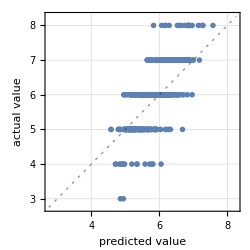
Predictor Measurements
Predictor method | RandomForest
Number of test examples | 490
Standard deviation | 0.619 ± 0.024
Standard deviation baseline | 0.876 ± 0.029
R-squared | 0.501 ± 0.051
Mean cross entropy | 0.94 ± 0.036
Single evaluation time | 6.52 ms/example
Batch evaluation speed | 2.09 examples/ms
-Graphics- |

```mathematica
p=Predict[standardizedTrainData->"WineQuality",PerformanceGoal->"Quality"];
pm=PredictorMeasurements[p,standardizedTestData]
```

### Standard NN

```mathematica
standardNet=StandardNet[16,4]
```

NetGraph[<>]

```mathematica
result=TrainStandardNet[standardNet,standardizedTrainData,standardizedTestData];
```

```mathematica
trainedStandardNet=result["TrainedNet"]
```

NetGraph[<>]

```mathematica
NetMeasurements[trainedStandardNet,standardizedTestData,{"RSquared","FractionVarianceUnexplained" ,"MeanDeviation","MeanSquare","StandardDeviation"}]
```

{0.413563,0.586437,0.526418,0.45012,0.67091}

```mathematica
standardPredictions=NetPredict[trainedStandardNet,standardizedTestData,"WineQuality"];
```

```mathematica
{MinMax[#["Prediction"]&/@standardPredictions],MinMax[#["Target"]&/@standardPredictions]}
```

{{3.91964,7.71983},{3,8}}

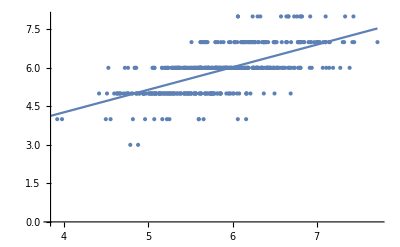

```mathematica
ResourceFunction["RegressionListPlot"][Values/@standardPredictions]
```

```mathematica
standardWeights=GetStandardWeights[trainedStandardNet];
```

```mathematica
standardNetSize=Quantity[Length[standardWeights]*32/1024.0,"Kilobytes"]
```

38. kB

## A neural logic network

```mathematica
{softNet,hardNet}=NeuralLogicNet[64]; (* This is OK for ~1000, but doesn't handle 4408 *)
```

```mathematica
NetFlatten[softNet]
```

NetGraph[<>]

```mathematica
result=Block[{td=Take[standardizedTrainData,All],vd=standardizedTestData},
TrainNeuralLogicNet[softNet,td,vd]
];
```

```mathematica
trainedNeuralLogicNet=result["TrainedNet"]
```

NetGraph[<>]

```mathematica
NetMeasurements[trainedNeuralLogicNet,standardizedTestData,{"RSquared","FractionVarianceUnexplained" ,"MeanDeviation","MeanSquare","StandardDeviation"}]
```

{0.414226,0.585774,0.490816,0.46586,0.68254}

```mathematica
neuralLogicPredictions=NetPredict[trainedNeuralLogicNet,standardizedTestData,"WineQuality"];
```

```mathematica
{MinMax[#["Prediction"]&/@neuralLogicPredictions],MinMax[#["Target"]&/@neuralLogicPredictions]}
```

{{4.5,7.6875},{3,8}}

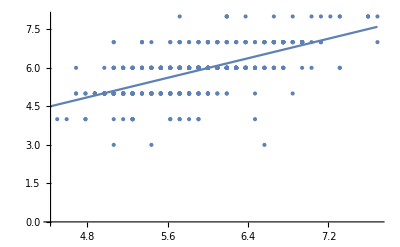

```mathematica
ResourceFunction["RegressionListPlot"][Values/@neuralLogicPredictions]
```

```mathematica
hnf=HardNetFunction[hardNet,trainedNeuralLogicNet];
hnbe=HardNetBooleanExpression[hnf,neuralLogicInputSize];
```

```mathematica
NeuralLogicPredict[data_,encoders_,targetName_,hardNetFunction_,featureLayer_]:=Module[{booleanPrediction},
booleanPrediction=ResourceFunction["DynamicMap"][<|
"Prediction"->N[First[encoders["WineQuality"]["DecoderFunction"][Boole[hardNetFunction[Harden[Normal[featureLayer[#]]]]]]]],
"Target"->#[targetName]
|>&,
Normal[data]
]
]
```

```mathematica
predictions=NeuralLogicPredict[standardizedTestData,encoders,"WineQuality",hnf,neuralLogicFeatureLayer];
```

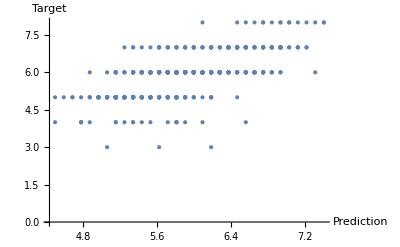

```mathematica
ListPlot[predictions,AxesLabel->Automatic]
```

```mathematica
neuralLogicWeights=GetNeuralLogicWeights[result["TrainedNet"]];
```

```mathematica
neuralLogicNetSize=Quantity[Length[neuralLogicWeights]/8/1024//N,"Kilobytes"]
```

7.97656 kB

```mathematica
standardNetSize/neuralLogicNetSize
```

80.

## Notes

## RealToBinary embedding layer

```mathematica
rbel=NetInitialize[RealToBinaryEmbeddingLayer[100]]
```

NetGraph[<>]

```mathematica
Values[Normal[testData[[1]]]]
```

{5,6.3,0.27,0.23,2.9,0.047,13.,100.,0.9936,3.28,0.43,9.8}

```mathematica
rbel[Values[Normal[testData[[1]]]]]
```

{1.,1.,1.,1.,1.,1.,1.,0.,1.,0.,1.,1.,0.,1.,1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,1.,0.,1.,1.,0.,0.,1.,1.,0.,1.,1.,1.,0.,0.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.,0.,1.,0.,1.,1.,0.,0.,1.,1.,0.,0.,1.,0.,0.,1.,0.,1.,0.,0.,1.,1.,0.,1.,0.,1.,1.,1.,0.,1.,1.,1.,0.,1.,1.,1.,1.,1.,0.,0.,0.,0.,1.,1.,1.}

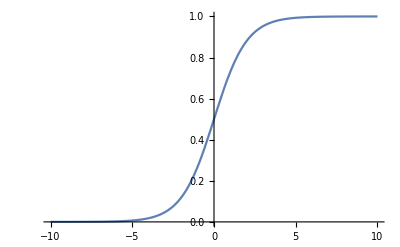

```mathematica
Plot[LogisticSigmoid[x],{x,-10,10}]
```

```mathematica
bctr=BinaryCountToReal[{0,1000}];
```

```mathematica
bctr[{1,1,1,1,0,0,0,0,0,0,1,1,1}]
```

{538.462}

```mathematica
bctrl=BinaryCountToRealLayer[13,{0,1000}]
```

NetGraph[<>]

```mathematica
bctrl[{1,1,1,1,0,0,0,0,0,0,1,1,1}]
```

538.462

```mathematica
bctrl[{0.8,0.52,0.6,0.85,0.1,0.2,0.3,0.4,0.45,0.49,0.99,0.65,0.62}]
```

538.462

```mathematica
{1,0,0,1,0,0,1,1}{128,64,32,16,8,4,2,1}
```

{128,0,0,16,0,0,2,1}

```mathematica
btr=BinaryToReal[8,{0.0,255.0}];
```

```mathematica
btr[{1,0,0,0,0,0,0,0}]
```

{255.}

```mathematica
btr[{1,0,0,0,0,1,1,0}]
```

{255.}

```mathematica
btr[{0,1,1,1,1,0,0,0}]
```

{239.063}

```mathematica
sbvtrl=SoftBitVectorToRealLayer[8,{0,255}]
```

NetGraph[<>]

```mathematica
{btr[{0,1,1,1,1,0,0,0}],sbvtrl[{0,1,1,1,1,0,0,0}]}
```

{{239.063},239.063}

```mathematica
{btr[Boole[Harden[{0.1,0.6,0.6,0.6,0.6,0,0,0}]]],sbvtrl[{0.1,0.6,0.6,0.6,0.6,0,0,0}]}
```

{{239.063},239.063}

## XOR layer

```mathematica
BooleanConvert[Xor[a,b],"CNF"]
```

(!a||!b)&&(a||b)

```mathematica
XorFunction[a_,b_]:=Min[Max[1-a,1-b],Max[a,b]]
```

```mathematica
XorFunction[0.1,0.8]
```

0.8

```mathematica
Clear[DifferentiableHardXOR]
```

```mathematica
HardXOR[b1_,b2_]:=Min[Max[1-b1,1-b2],Max[b1,b2]]
DifferentiableHardXOR[b_List]:=Fold[HardXOR[#1,#2]&,0.0,b]
```

```mathematica
DifferentiableHardXOR[{0.1,0.8}]
```

0.8

```mathematica
XorFunction[XorFunction[0.1,0.8],0.9]
```

0.2

```mathematica
DifferentiableHardXOR[{0.1,0.8,0.9}]
```

0.2

```mathematica
DifferentiableHardXOR[{0.1,0.8,0.9,0.51}]
```

0.51

```mathematica
fl=FunctionLayer[HardXOR[#Input,#State]&,"Output"->{}]
```

FunctionLayer[<>]

```mathematica
nfo=NetFoldOperator[fl]
```

NetFoldOperator[<>]

```mathematica
nfo[{0.1,0.8,0.9}]
```

{0.1,0.8,0.2}

```mathematica
nfo[{0.1,0.8,0.9,0.51}]
```

{0.1,0.8,0.2,0.51}

```mathematica
nfo[{0.1,0.8,0.9},NetPort[All,"States"]]
```

<|{State}→0.2|>

```mathematica
nfo[{0.1,0.8,0.9,0.51},NetPort[All,"States"]]
```

<|{State}→0.51|>

```mathematica
sll=SequenceLastLayer[]
```

SequenceLastLayer[<>]

```mathematica
sll[{0.10000000149011612,0.800000011920929,0.19999998807907104,0.5099999904632568}]
```

0.51

```mathematica
Manipulate[Plot[XorFunction[a,b],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2},{1/2}}],{a,0,1}]
```

```mathematica
BooleanConvert[Xor[a,b,c],"CNF"]
```

(!a||!b||c)&&(!a||b||!c)&&(a||!b||!c)&&(a||b||c)

```mathematica
BooleanConvert[Xor[a,b,c,d],"CNF"]
```

(!a||!b||!c||!d)&&(!a||!b||c||d)&&(!a||b||!c||d)&&(!a||b||c||!d)&&(a||!b||!c||d)&&(a||!b||c||!d)&&(a||b||!c||!d)&&(a||b||c||d)

```mathematica
Xor[a,b,c]==Xor[Xor[a,b],c]
```

True

```mathematica
Xor[False,False]
```

False

```mathematica
Xor[True,False]
```

True

```mathematica
Xor[False,True]
```

True

```mathematica
Xor[True,True]
```

False

```mathematica
BooleanConvert[Xor[b1,b2,b3,b4,b5,b6,b7],"CNF"]
```

(!b1||!b2||!b3||!b4||!b5||!b6||b7)&&(!b1||!b2||!b3||!b4||!b5||b6||!b7)&&(!b1||!b2||!b3||!b4||b5||!b6||!b7)&&(!b1||!b2||!b3||!b4||b5||b6||b7)&&(!b1||!b2||!b3||b4||!b5||!b6||!b7)&&(!b1||!b2||!b3||b4||!b5||b6||b7)&&(!b1||!b2||!b3||b4||b5||!b6||b7)&&(!b1||!b2||!b3||b4||b5||b6||!b7)&&(!b1||!b2||b3||!b4||!b5||!b6||!b7)&&(!b1||!b2||b3||!b4||!b5||b6||b7)&&(!b1||!b2||b3||!b4||b5||!b6||b7)&&(!b1||!b2||b3||!b4||b5||b6||!b7)&&(!b1||!b2||b3||b4||!b5||!b6||b7)&&(!b1||!b2||b3||b4||!b5||b6||!b7)&&(!b1||!b2||b3||b4||b5||!b6||!b7)&&(!b1||!b2||b3||b4||b5||b6||b7)&&(!b1||b2||!b3||!b4||!b5||!b6||!b7)&&(!b1||b2||!b3||!b4||!b5||b6||b7)&&(!b1||b2||!b3||!b4||b5||!b6||b7)&&(!b1||b2||!b3||!b4||b5||b6||!b7)&&(!b1||b2||!b3||b4||!b5||!b6||b7)&&(!b1||b2||!b3||b4||!b5||b6||!b7)&&(!b1||b2||!b3||b4||b5||!b6||!b7)&&(!b1||b2||!b3||b4||b5||b6||b7)&&(!b1||b2||b3||!b4||!b5||!b6||b7)&&(!b1||b2||b3||!b4||!b5||b6||!b7)&&(!b1||b2||b3||!b4||b5||!b6||!b7)&&(!b1||b2||b3||!b4||b5||b6||b7)&&(!b1||b2||b3||b4||!b5||!b6||!b7)&&(!b1||b2||b3||b4||!b5||b6||b7)&&(!b1||b2||b3||b4||b5||!b6||b7)&&(!b1||b2||b3||b4||b5||b6||!b7)&&(b1||!b2||!b3||!b4||!b5||!b6||!b7)&&(b1||!b2||!b3||!b4||!b5||b6||b7)&&(b1||!b2||!b3||!b4||b5||!b6||b7)&&(b1||!b2||!b3||!b4||b5||b6||!b7)&&(b1||!b2||!b3||b4||!b5||!b6||b7)&&(b1||!b2||!b3||b4||!b5||b6||!b7)&&(b1||!b2||!b3||b4||b5||!b6||!b7)&&(b1||!b2||!b3||b4||b5||b6||b7)&&(b1||!b2||b3||!b4||!b5||!b6||b7)&&(b1||!b2||b3||!b4||!b5||b6||!b7)&&(b1||!b2||b3||!b4||b5||!b6||!b7)&&(b1||!b2||b3||!b4||b5||b6||b7)&&(b1||!b2||b3||b4||!b5||!b6||!b7)&&(b1||!b2||b3||b4||!b5||b6||b7)&&(b1||!b2||b3||b4||b5||!b6||b7)&&(b1||!b2||b3||b4||b5||b6||!b7)&&(b1||b2||!b3||!b4||!b5||!b6||b7)&&(b1||b2||!b3||!b4||!b5||b6||!b7)&&(b1||b2||!b3||!b4||b5||!b6||!b7)&&(b1||b2||!b3||!b4||b5||b6||b7)&&(b1||b2||!b3||b4||!b5||!b6||!b7)&&(b1||b2||!b3||b4||!b5||b6||b7)&&(b1||b2||!b3||b4||b5||!b6||b7)&&(b1||b2||!b3||b4||b5||b6||!b7)&&(b1||b2||b3||!b4||!b5||!b6||!b7)&&(b1||b2||b3||!b4||!b5||b6||b7)&&(b1||b2||b3||!b4||b5||!b6||b7)&&(b1||b2||b3||!b4||b5||b6||!b7)&&(b1||b2||b3||b4||!b5||!b6||b7)&&(b1||b2||b3||b4||!b5||b6||!b7)&&(b1||b2||b3||b4||b5||!b6||!b7)&&(b1||b2||b3||b4||b5||b6||b7)